Leaf Classifier

Chetty Harish

Last First

NMIMS- Mukesh Patel School of Technology, Management and Engineering.

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: The goal of the project is to classify leaves on the basis of their species using a Convolution Neural Network (CNN) model.

SUMMARY OF WORK: A dataset of different species of leaves from Northeastern United States and Canada was taken and was split into training and validation sets. A Convolutional Neural Network (CNN) model was developed for the application of Deep learning in Image Processing. The network was trained on this dataset and a Leaf Classifier was developed.

RESULTS AND FUTURE  WORK: The network is able to classify the leaf on the basis of it’s species most of the time. With more training and parameters, the accuracy level of the classifier can be improved. This network and be useful on a larger dataset with species of leaves from worldwide and thus has a vast range of possibilities to classify from. With more training and a large variety of datasets a lot can be achieved in the future.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

```mathematica
trainingSet=Import["C:\\Users\\haris\\OneDrive\\Documents\\projectDocument\\trainingSet.mx"];
RandomSample[trainingSet,5]
```

{File[C:\Users\haris\OneDrive\Documents\trainingSetData\13002220991863.jpg]→Tilia cordata,File[C:\Users\haris\OneDrive\Documents\trainingSetData\7224864682430374890.jpg]→Robinia pseudo-acacia,File[C:\Users\haris\OneDrive\Documents\trainingSetData\13002166696244.jpg]→Prunus virginiana,File[C:\Users\haris\OneDrive\Documents\trainingSetData\13001152969446.jpg]→Acer palmatum,File[C:\Users\haris\OneDrive\Documents\trainingSetData\5608198468904594855.jpg]→Juglans nigra}

```mathematica
NetModel["SqueezeNet V1.1 Trained on ImageNet Competition Data"]
```

NetChain[]

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

The Goal of the project was to create a classifier which correctly classifies the species of the leaf while taking image file as the input and giving the corresponding species of the leaf, the image belongs to. To do so, a Convolutional Neural Network Model was taken into account. The Network Architecture referred to was “SqueezeNet V1.1 Trained on ImageNet Competition Data”. The Dataset consisted of 184 different species, thus the network was designed in the way that it gives out the result distributed among 184 different species and one with the highest probability be interpreted as the species of the image.
The network is then trained over a training data set of 9727 images of different leafs with a validation dataset of 2498 images to validate the training of the network. The Accuracy obtained is 91.7%, however is this due to over-fitting during the training. This is mainly due the less amount of test dataset present.

Code

https://github.com/roronoaharish/WSS-17/tree/master/Project

Code of the Project :

Importing the Data set from the local machine and creating a valid dataset as “File-> Class”.

```mathematica
data = SemanticImport["C:\\Users\\haris\\Desktop\\leafDataSet\\leafsnap-dataset-images.txt",<|"image_path"->Automatic,"species"->"String","source"->"String"|>];
actualData = GroupBy[Normal[data],Last->(Slot["image_path"]->Slot["species"]&)]["field"];
addFullPath[x_] := FileNameJoin[{"","Users","haris","Desktop","leafDataSet",x}];
actualData = Normal[KeyMap[File@*addFullPath, Association[actualData]]];
fileBySpiecies=GroupBy[actualData,Last->First];
```

Function to create more data as the current data is not enough and storing it in a directory called createdData.

```mathematica
smallSets=Select[fileBySpiecies,Length[#]<40&]; (* Creating Data for dataset of classes less than 40*)
SetDirectory["createdData"];
transformationList={ImageRotate, ImageReflect};
applyFunction[key_,value_]:=key->Flatten@Table[	
						Export[StringJoin[ToString[Hash[#]],".jpg"],#]&/@Through[transformationList[img] ],
						{img,Import/@value}]
createdData=Map[File@*AbsoluteFileName,KeyValueMap[applyFunction,smallSets],{3}];
ResetDirectory[];
```

Merging the created data and the actual data.

```mathematica
finalData=Flatten[Join[actualData, Map[Reverse,Thread/@createdData,{2}]]];
```

Separating data into training and validation dataset.

```mathematica
set1=Keys@GroupBy[Import["C:\\Users\\haris\\OneDrive\\Documents\\finaldata.m"],Values,Keys];
set2=Values@GroupBy[Import["C:\\Users\\haris\\OneDrive\\Documents\\finaldata.m"],Values,Keys];
trainingSet=Take[#,Floor[.8*Length[#]]]&/@set2;
trainingSet=Thread[set1->trainingSet];
trainingSet=Flatten@Map[Reverse,Thread/@trainingSet,{2}];
validationSet= Complement[finalData,trainingSet];
$classes=Union[finaldata[[All,2]]]
```

Moving All the training Set and the Validation Set to a single Main Directory and Sub Directories as trainingSetData and validationSetData.

```mathematica
ParallelMap[CopyFile[#, "C:\\Users\\haris\\OneDrive\\Documents\\trainingSetData\\"<>FileNameTake[#]]&, paths];
trainingFiles=File/@FileNames["C:\\Users\\haris\\OneDrive\\Documents\\trainingSetData\\*"];
setNames=FileBaseName/@trainingSet[[All,1]];
fileNames = FileBaseName/@trainingFiles[[All,1]];
f := Function[
	Block
	[
		{base, pos},
		
		base = FileBaseName[#];
		pos = Position[setNames, base][[1,1]];
		# -> trainingSet[[pos, 2]]
	]
]
training=ParallelMap[f,trainingFiles]
paths=Keys[validationSet][[All,1]];
ParallelMap[CopyFile[#, "C:\\Users\\haris\\OneDrive\\Documents\\validationSetData\\"<>FileNameTake[#]]&, paths];
setNames=FileBaseName/@validationSet[[All,1]];
validationFiles=File/@FileNames["C:\\Users\\haris\\OneDrive\\Documents\\validationSetData\\*"];
fileNames = FileBaseName/@validationFiles[[All,1]];
f := Function[
	Block
	[
		{base, pos},
		
		base = FileBaseName[#];
		pos = Position[setNames, base][[1,1]];
		# -> validationSet[[pos, 2]]
	]
]
validation=ParallelMap[f,validationFiles]
```

Creating a Net design.

```mathematica
squeezeNet=NetModel["SqueezeNet V1.1 Trained on ImageNet Competition Data"];

finalNet=NetChain[Join[Association["imgaug10"->ImageAugmentationLayer[{227,227},"ReflectionProbabilities"-> {0.5,0.5}]],
Normal@Drop[squeezeNet,-5],
Association[
"conv10"->ConvolutionLayer[184,{1,1}],
"relu_conv10"->Ramp,
"pool10"->AggregationLayer[Mean],
"probabilities"->SoftmaxLayer[]
]],
"Input"->NetEncoder[{"Image",{300,300},ColorSpace->"RGB"}],
"Output"->  NetDecoder[{"Class",$classes}]
]
```

Creating “.MX” and “.WLNET” files for remote training.

```mathematica
trainingOoC= Import[FileNameJoin[{Directory[],"finalTrainingSet.m"}]];
validation=  Import[FileNameJoin[{Directory[],"finalValidationSet.m"}]];
Export["trainingSetIndex.mx",trainingOoC,"MX"]
Export["validationSetIndex.mx",validation,"MX"]
Export["net.wlnet",finalNet]
```

Training of the Network.(Script)

```mathematica
classesPath = FileNameJoin[{Directory[],"classes.m"}];
$classes = Import[classesPath];
trainingSetIndexPath= FileNameJoin[{Directory[],"trainingSetIndex.mx"}];
validationSetIndexPath= FileNameJoin[{Directory[],"validationSetIndex.mx"}];
netPath = FileNameJoin[{Directory[],"net.wlnet"}];
Length@Normal@netPath;
checkpointsPath= FileNameJoin[{Directory[],"Checkpoint"}]; 	
netPath;
net = Import@netPath;
trainingSetIOFiles  = Activate @ Import @ trainingSetIndexPath;
validationSetIOFiles  = Activate @ Import @ validationSetIndexPath

(* Round 1 of training *)
trainedNet = NetTrain[
	net,
	trainingSetIOFiles,
	ValidationSet -> validationSetIOFiles,
	TrainingProgressCheckpointing -> {
		"Directory", 
		checkpointsPath, 
		"Interval" -> Quantity[1, "Hours"]
	},
	LearningRateMultipliers -> {"conv10"->1, _ -> None}
]


Export[FileNameJoin@{checkpointsPath, "final.wlnet"}, trainedNet];
```

Round 2 of training.

```mathematica
netPath = FileNameJoin[{Directory[],"Checkpoint","final.wlnet"}];
trainedNet = NetTrain[
	net,
	trainingSetIOFiles,
	ValidationSet -> validationSetIOFiles,
	TrainingProgressCheckpointing -> {
		"Directory", 
		checkpointsPath, 
		"Interval" -> Quantity[1, "Hours"]
	},
	MaxTrainingRounds-> 100,
	LearningRateMultipliers -> {"conv10"->1, "fire7"->0.03,_ -> 0.01}
]


Export[FileNameJoin@{checkpointsPath, "2017-07-05T02_38_18_0_100_12200_5.04e-2_3.85e-1.wlnet"}, trainedNet];
```

Function to find the accuracy of the network.

```mathematica
results=net/@validationSetIOFiles[[All,1]];

expected=validationSetIOFiles[[All,2]];
f[x_,y_]:= N[Count[
				MapThread[
						SameQ,
						{x,y}
						   ],
				True]/ Length@validationSetIOFiles];
f[results,expected]
```

Written Content / Lesson Plans

Conclusions in Detail

It can be concluded that, a large number of training data is needed to train the network and a good amount of test data set is needed to measure the network accuracy. Since the dataset provided to such a complex network is small, the chances of over-fitting increases. This network can be used on a large amount of dataset with

All Visualizations

Size of the data set after creating more data.

```mathematica
Histogram[GroupBy[finalData,Last->First,Length],{5}]
```

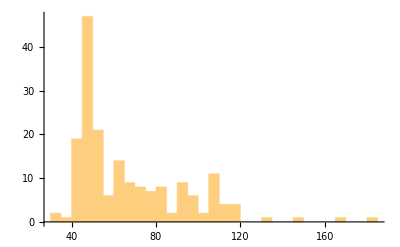

Random sample of the training Set.

```mathematica
Grid[Partition[Thread[Import/@RandomSample[trainingSet,4][[All,1]]->RandomSample[trainingSet,4][[All,2]]],2],Alignment->Left]
```

```mathematica
{{-Graphics-->"Amelanchier arborea", -Graphics-->"Tilia tomentosa"}, {-Graphics-->"Evodia daniellii", -Graphics-->"Styrax japonica"}}
```

Data Sources Links/References

“Leafsnap: A Computer Vision System for Automatic Plant Species Identification,”
Neeraj Kumar,Peter N.Belhumeur,Arijit Biswas,David W.Jacobs,W.John Kress,Ida C.Lopez,João V.B.Soares,Proceedings of the 12th European Conference on Computer Vision (ECCV),October 2012

Future Directions

The network to be trained on a big amount of data set and can used for all the species of leaf present on earth. The drawback faced here was the the data set present is really small. In future the network can be trained on big amount of data set with good amount of test set available and thus can be improved exponentially.

Background Info Links/References

Plant Leaf Recognition Using a Convolution Neural Network Wang-Su Jeon1 and Sang-Yong Rhee2 1Department of IT Convergence Engineering, Kyungnam University, Changwon, Korea 2Department of Computer Engineering, Kyungnam University, Changwon, Korea

Keywords

Leaf Classifier

Convolutional Neural Networks

Deep Learning

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```